```mathematica
F[r_]:=Factorial[r]/(2^(r/2)*Factorial[r/2])
```

```mathematica
Table[{r,F[r]},{r,2,10,2}]
```

{{2,1},{4,3},{6,15},{8,105},{10,945}}

```mathematica
La
```

La

```mathematica
Integrate[Integrate[DiracDelta[x+y],{x,-1,1}],{y,-1,1}]
```

2

```mathematica
- FullSimplify[( 1/2+Sqrt[1/4-Abs[x]^2(1- Abs[x]^2)]) * Log[ 1/2+Sqrt[1/4-Abs[x]^2(1- Abs[x]^2)]] + ( 1/2-Sqrt[1/4-Abs[x]^2(1- Abs[x]^2)]) * Log[ 1/2-Sqrt[1/4-Abs[x]^2(1- Abs[x]^2)]] ]
```

-ArcTanh[1-2 x Conjugate[x]] (1-2 x Conjugate[x])-1/2 Log[Abs[x]^2-Abs[x]^4]

```mathematica
Integrate[-ArcTanh[1-2 x Conjugate[x]] (1-2 x Conjugate[x])-1/2 Log[Abs[x]^2-Abs[x]^4],{x,0,1}]
```

-4/3 (-1+Log[2])

```mathematica
N[-4/3 (-1+Log[2]),8]
```

0.40913709

```mathematica
-Integrate[x*Exp[-x^2/2]*(x^2*Log[x^2]+(1-x^2)*Log[1-x^2]), {x,0,1},Assumptions->x∈Reals]/(1-1/(√ⅇ))
```

-(2 (-((1+√ⅇ) EulerGamma)+ExpIntegralEi[1/2]+Log[2]+√ⅇ (ExpIntegralEi[-1/2]+Log[2])))/((1-1/(√ⅇ)) √ⅇ)

```mathematica
N[-(2 (-((1+√ⅇ) EulerGamma)+ExpIntegralEi[1/2]+Log[2]+√ⅇ (ExpIntegralEi[-1/2]+Log[2])))/((1-1/(√ⅇ)) √ⅇ),10]
```

0.4982739535

```mathematica
Integrate[x*Exp[-x^2/2], {x,0,1},Assumptions->x∈Reals]
```

1-1/(√ⅇ)

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*x^2/(x^2+y^2+z^2)*Log[x^2/(x^2+y^2+z^2)],{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->10]-NIntegrate[1/Pi^3 * Exp[-x^2-y^2-a^2-b^2-c^2-d^2]*(1+2*(x*y+a*b)/(x^2+y^2+a^2+b^2+c^2+d^2))*Log[1+2*(x*y+a*b)/(x^2+y^2+a^2+b^2+c^2+d^2)], {x,-∞,∞},{y,-∞,∞},{a,-∞,∞},{b,-∞,∞},{c,-∞,∞},{d,-∞,∞}, WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.09087851122 and 0.000581015403 for the integral and error estimates.

0.186899717

```mathematica
Rationalize[0.18689971657320970484461932444560727683`9.704986465617816,10^-6]
```

214/1145

```mathematica
-2*NIntegrate[x*y*Exp[-(x^2+y^2)/2]*x^2/(x^2+y^2)*Log[x^2/(x^2+y^2)],{x,0,∞}, {y,0,∞}]
```

0.5

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*x^2/(x^2+y^2+z^2)*Log[x^2/(x^2+y^2+z^2)],{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->16]
```

0.2777777776057834

```mathematica
-4*NIntegrate[x*y*z*t*Exp[-(x^2+y^2+z^2+t^2)/2]*x^2/(x^2+y^2+z^2+t^2)*Log[x^2/(x^2+y^2+z^2+t^2)],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},WorkingPrecision->15]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.270833335428663 and 1.0176633969514×10^-6 for the integral and error estimates.

1.08333334171465

```mathematica
-5*NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*x^2/(x^2+y^2+z^2+t^2+w^2)*Log[x^2/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.25666731922277668618 and 0.000013037813116167567386 for the integral and error estimates.

1.2833365961138834309

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.25666731922277668618 and 0.000013037813116167567386 for the integral and error estimates.

0.25666731922277668618

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.31333343855359936198 and 0.000020568029257935534962 for the integral and error estimates.

0.31333343855359936198

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2+z^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2+z^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.27000003697027177065 and 0.000014787936562812687123 for the integral and error estimates.

0.27000003697027177065

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*Exp[-(x^2+y^2+z^2+t^2+w^2)/2]*(x^2+y^2+z^2+t^2)/(x^2+y^2+z^2+t^2+w^2)*Log[(x^2+y^2+z^2+t^2)/(x^2+y^2+z^2+t^2+w^2)]],{x,0,∞}, {y,0,∞},{z,0,∞},{t,0,∞},{w,0,∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.16000083866797140165 and 0.000010725529490965252467 for the integral and error estimates.

0.16000083866797140165

```mathematica
FindGeneratingFunction[{1/4,5/18,26/144,154/600,1044/4320},x]
```

FindGeneratingFunction[{1/4,5/18,13/72,77/300,29/120},x]

```mathematica
Rationalize[0.2566673192227766861819622403610262323`20.+0.0,10^-5]
```

77/300

```mathematica
Rationalize[0.31333343855359936198`20.+0.0,10^-5]
```

47/150

```mathematica
Rationalize[0.16000083866797140165+0.0,10^-5]
```

4/25

```mathematica
-NIntegrate[FullSimplify[x*y*z*t*w*u*v*Exp[-(x^2+y^2+z^2+t^2+w^2+u^2+v^2)/2]*x^2/(x^2+y^2+z^2+t^2+w^2+u^2+v^2)*Log[x^2/(x^2+y^2+z^2+t^2+w^2+u^2+v^2)]],{x,10^(-4),∞}, {y,10^(-4),∞},{z,10^(-4),∞},{t,10^(-4),∞},{w,10^(-4),∞}, {u,10^(-4),∞}, {v,10^(-4),∞},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.22757141405903968488 and 0.00069341757566486985772 for the integral and error estimates.

0.22757141405903968488

```mathematica
Rationalize[0.22757141405903968488*7,10^-4]
```

137/86

```mathematica
N[15/18,10]
```

0.8333333333

```mathematica
Integrate[x*Exp[-x^2/2]*a^4/(x^2+b+a^2)^2,{x,0,∞},Assumptions->a∈Reals,Assumptions->b∈Reals]
```

ConditionalExpression[a^4 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)])), ]

```mathematica
Simplify[a^2 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)]))]
```

a^2 (1/(2 (a^2+b))+1/4 ⅇ^(1/2 (a^2+b)) (CoshIntegral[1/2 (-a^2-b)]-Log[-a^2-b]+Log[a^2+b]-SinhIntegral[1/2 (a^2+b)]))

```mathematica
NIntegrate[(x*y*z*t)*Exp[-(x^2+y^2+z^2+t^2)/2]*(x*y*z*t)^2/(x^2+y^2+z^2+t^2)^4,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, WorkingPrecision->12]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00119047607441

```mathematica
Ap[x_,y_,z_]:=1/2+1/2*Sqrt[1-4*x^2*z^2/(x^2+y^2+z^2)^2]
```

```mathematica
Am[x_,y_,z_]:=1/2-1/2*Sqrt[1-4*x^2*z^2/(x^2+y^2+z^2)^2]
```

```mathematica
-NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*(Ap[x,y,z]*Log[Ap[x,y,z]]+Am[x,y,z]*Log[Am[x,y,z]]),{x,0,∞}, {y,0,∞},{z,0,∞},WorkingPrecision->20,Exclusions->{0,0,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.2850220624915902623620493720206354628109800928226296192713581029455553 and 1.403416516981714857961508438111766594570930462415143586330282027283369×10^-6 for the integral and error estimates.

0.28502206249159026236

```mathematica
n:=1
```

```mathematica
Table[{n,NIntegrate[x*y*Exp[-(x^2+y^2)/2]*((x^4+y^4)/(x^2+y^2)^(2))^n,{x,0,∞}, {y,0,∞},PrecisionGoal->10,WorkingPrecision->20],NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*((x^4+y^4+z^4)/(x^2+y^2+z^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},PrecisionGoal->10,WorkingPrecision->20],NIntegrate[x*y*z*t*Exp[-(x^2+y^2+z^2+t^2)/2]*((x^4+y^4+z^4+t^4)/(x^2+y^2+z^2+t^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞},,PrecisionGoal->10,WorkingPrecision->20],NIntegrate[x*y*z*t*u*Exp[-(x^2+y^2+z^2+t^2+u^2)/2]*((x^4+y^4+z^4+t^4+u^4)/(x^2+y^2+z^2+t^2+u^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞},PrecisionGoal->10,WorkingPrecision->15],NIntegrate[x*y*z*t*u*v*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2)/2]*((x^4+y^4+z^4+t^4+u^4+v^4)/(x^2+y^2+z^2+t^2+u^2+v^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞},PrecisionGoal->10,WorkingPrecision->12],NIntegrate[x*y*z*t*u*v*w*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2+w^2)/2]*((x^4+y^4+z^4+t^4+u^4+v^4+w^4)/(x^2+y^2+z^2+t^2+u^2+v^2+w^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞}, {w,0,∞},PrecisionGoal->10,WorkingPrecision->10]},{n,3,4}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.1523809524246784779933605449107552554369983213653176916598650176398263 and 9.070452059117364535429050615952859376863433307757864373294696758204557×10^-9 for the integral and error estimates.

NIntegrate::ilim: Invalid integration variable or limit(s) in Null.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0460316777054574 and 5.77859092942332×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0288534148351 and 0.0000221368617215 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ilim: Invalid integration variable or limit(s) in Null.

$Aborted

```mathematica
{4,0.46666666666658422165696907595220009627`20.,0.26666666667995411073664221607649627225`20.,0.17142858863266707467840801984473041487`20.,0.1190476386475898213260984233498802864`15.,0.08730317566257726134722166198716768986`15.,0.0666589154693273006864198360639984233`15.},{6,0.34285714285716211563248529124275776959`20.,0.15238095242467847799336054491075525544`20.,0.07936507893551125260112733367017482958`20.,0.04603167770545738271988434670497092927`15.,0.02885341483513232363163928577437349836`15.,0.01920398052001276256617272510844477154`15.},{8,0.26349206349208076146475013261227513197`20.,0.09333333379521981808785241394518002014`20.,0.03988456121363357368946833862243150562`20.,0.01943242619506415925682622246683176051`15.,0.01043438802830827462783407765296639584`15.,0.0060412440598467638567590782653416553`15.}}
```

4/87

```mathematica
Table[{n,NIntegrate[x*y*Exp[-(x^2+y^2)/2]*((x^4)/(x^2+y^2)^(2))^n,{x,0,∞}, {y,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*((x^4)/(x^2+y^2+z^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*Exp[-(x^2+y^2+z^2+t^2)/2]*((x^4)/(x^2+y^2+z^2+t^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞},WorkingPrecision->20],NIntegrate[x*y*z*t*u*Exp[-(x^2+y^2+z^2+t^2+u^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞},WorkingPrecision->15],NIntegrate[x*y*z*t*u*v*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2+v^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞},WorkingPrecision->12],NIntegrate[x*y*z*t*u*v*w*Exp[-(x^2+y^2+z^2+t^2+u^2+v^2+w^2)/2]*((x^4)/(x^2+y^2+z^2+t^2+u^2+v^2+w^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞}, {t,0,∞}, {u,0,∞}, {v,0,∞}, {w,0,∞},WorkingPrecision->10]},{n,2,4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.066666666055160363536 and 1.1487422971016100848×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.028571429691979055337 and 6.4518367010550848641×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0142857167583558 and 8.62729480083682×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

```mathematica
Rationalize[1*{1,0.34285714285716211563248529124275776959`20.,0.15238095242467847799336054491075525544`20.,0.07936507893551125260112733367017482958`20.,0.04603167770545738271988434670497092927`15.,0.02885341483513232363163928577437349836`15.,0.01920398052001276256617272510844477154`15.},10^(-4)]
```

{1,12/35,16/105,5/63,4/87,3/104,1/52}

```mathematica
FindSequenceFunction[{1,11/32,5/33,2/25,1/22},x]
```

FindSequenceFunction[{1,11/32,5/33,2/25,1/22},x]

```mathematica
FindSequenceFunction[{1,1/3,1/6,1/10,1/15,1/21,1/28},x]
```

2/(x (1+x))

```mathematica
Apart[(5+x)/((1+x) (2+x) (3+x))]
```

2/(1+x)-3/(2+x)+1/(3+x)

```mathematica
Table[6*Factor[2/(1+x)-3/(2+x)-4/(3+x)+5/(4+x)+1/(5+x)],{x,1,5}]
```

{1,39/70,61/140,163/420,38/105}

```mathematica
FindSequenceFunction[{1,2/3,7/15,12/35,83/315,146/693},n]
```

```mathematica
FindSequenceFunction[{1,1/2,4/15,16/105,7/75,47/770},n]
```

```mathematica
FindSequenceFunction[{1,1/2,4/15,16/105,7/75,47/770,27/638},n]
```

```mathematica
FindSequenceFunction[{1,1/2,4/15,16/105,7/75,13/213,8/189,7/227,7/299},n]
```

FindSequenceFunction[{1,1/2,4/15,16/105,7/75,13/213,8/189,7/227,7/299},n]

```mathematica
FindSequenceFunction[{1,2/3,7/15,12/35,83/315,146/693,523/3003},n]
```

-(2^(1-n) (ⅈ √π n!+2^n (1/2 (-1+2 n))! Hypergeometric2F1[1,1/2+n,1+n,2]) Pochhammer[1,-1+n])/(√π n! Pochhammer[3/2,-1+n])

```mathematica
Table[NIntegrate[x*y*z*Exp[-(x^2+y^2+z^2)/2]*((x^4+y^4+z^4)/(x^2+y^2+z^2)^(2))^n,{x,0,∞}, {y,0,∞}, {z,0,∞},PrecisionGoal->20],{n,0,8}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.16501×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.5 and 1.28825×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.266667 and 1.09516×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{1.,0.5,0.266667,0.152381,0.0933333,0.061039,0.0423196,0.0308358,0.023408}

```mathematica
Rationalize[{1.0000000000105012,0.5000000000101862,0.26666666667996014,0.15238095242468214,0.09333333379521588,0.06103896107029914,0.042319585170905866,0.030835830816556904,0.02340796457646466},10^(-5)]
```

{1,1/2,4/15,16/105,7/75,13/213,8/189,7/227,7/299}

```mathematica
RSolve[f[x]-(x-1)/(x-1+2n)*f[x-1]==0,f[x],x]
```

{{f[x]→(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]}}

```mathematica
Simplify[(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]]
```

(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]

```mathematica
FunctionExpand[(C[1] Pochhammer[1,-1+x])/Pochhammer[1+2 n,-1+x]]
```

(C[1] Gamma[1+2 n] Gamma[x])/Gamma[2 n+x]

```mathematica
y-y*Sum[(Gamma[1+2 n] Gamma[x]*y^n)/(x^(2n-1)Gamma[2 n+x]*n*(n+1)),{n,1,∞}]/Log[2]
```

y-(y^2 Gamma[x] HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x Gamma[2+x] Log[2])

```mathematica
FullSimplify[y-(y^2 Gamma[x] HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x Gamma[2+x] Log[2])]
```

y-(y^2 HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},y/x^2])/(x^2 (1+x) Log[2])

```mathematica
F[x_,f_]:=2*f-2*(f^2 HypergeometricPFQ[{1,1,3/2,2},{3,1+x/2,3/2+x/2},f/x^2])/(x^2 (1+x) Log[2])
```

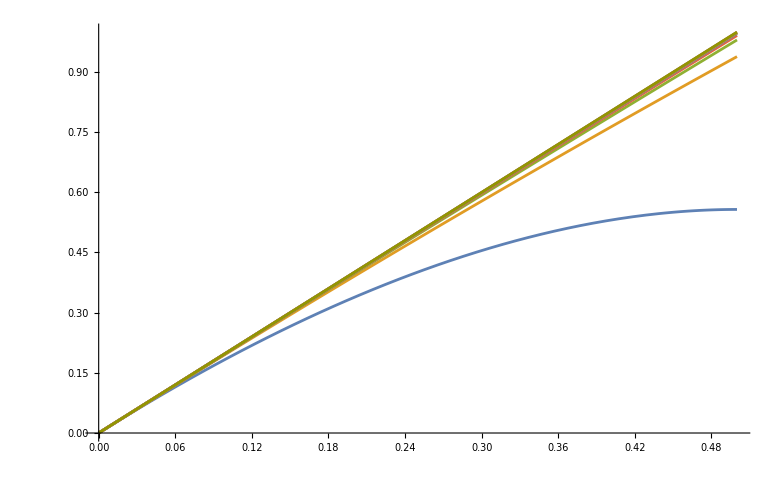

```mathematica
Plot[Evaluate[Table[F[n,x],{n,1,10}]],{x,0,0.5}]
```

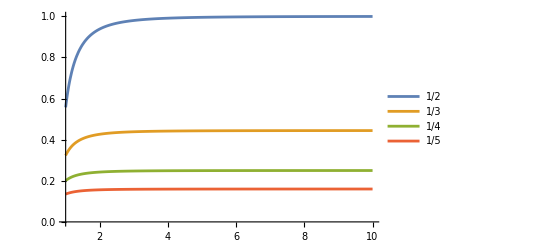

Power::infy: Infinite expression 1/0 encountered.

Integrate::idiv: Integral of -1/2 Log[(1-2 x^2+√(1-4 Power[«2»]))/(2 x)] does not converge on {0,∞}.

```mathematica
Plot[Evaluate[Table[2/n*F[x, 1/n],{n,2,5}]],{x,1,10},PlotLegends->{f=1/2,f=1/3,f=1/4,f=1/5}]
```

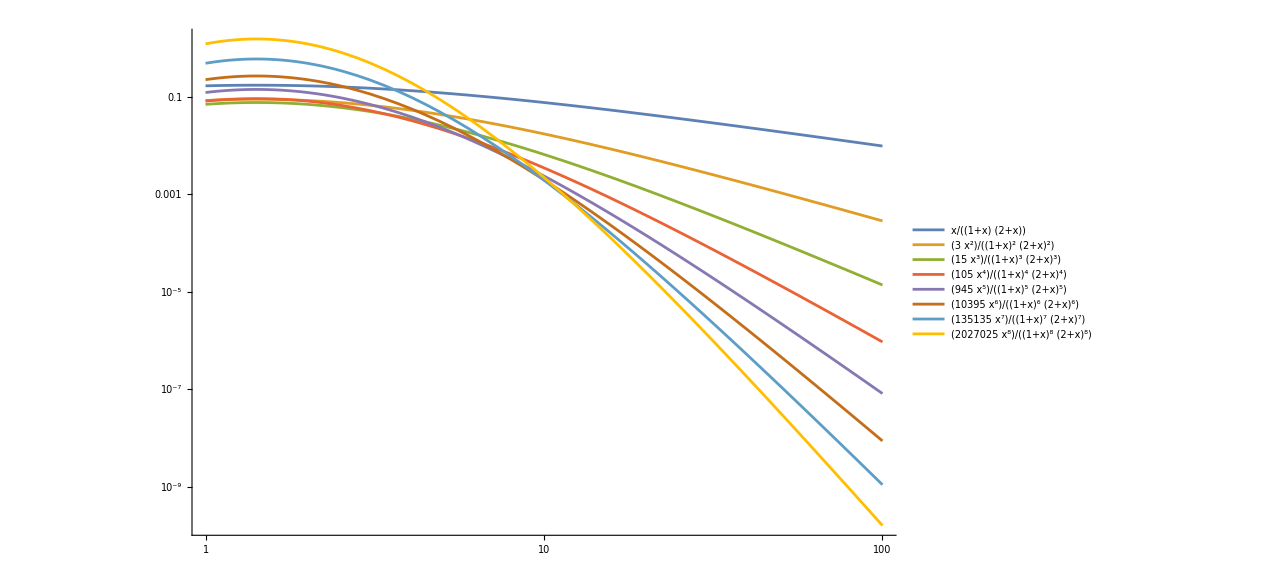

```mathematica
LogLogPlot[Evaluate[Table[(2r)!/(2^r*r!)*x^r/((1+x)^r(2+x)^r),{r,1,8}]],{x,1,100}, PlotLegends->"Expressions"]
```

```mathematica
Factor[Sum[(l-1)^2,{l,2,La+1}]+Sum[(2*La-l+1)^2,{l,La+2,2*La}]]
```

1/3 La (1+2 La^2)

```mathematica
Table[Sum[KroneckerDelta[i1+i6,i5+i7]*KroneckerDelta[i2+i4,i1+i3]*KroneckerDelta[i5+i3,i2+i4]*KroneckerDelta[i6,i7],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La}],{La,1,10}]
```

{1,12,57,176,425,876,1617,2752,4401,6700}

```mathematica
FindGeneratingFunction[{1,10,45,136,325,666,1225,2080,3321,5050,7381,10440,14365,19306,25425},x]
```

(-1-5 x-5 x^2-x^3)/(-1+x)^5

```mathematica
Table[Sum[KroneckerDelta[i1+i7,i2+i8]*KroneckerDelta[i2+i3,i1+i6]*KroneckerDelta[i4+i8,i3+i5]*KroneckerDelta[i5+i6,i4+i7],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,16,103,408,1209,2960,6335,12272}

```mathematica
Chi[q1_,q2_,La_]:=1/L*Sum[Exp[i*2*Pi*(q1-q2)/L*i],{i,1,La}]
```

```mathematica
Table[Sum[KroneckerDelta[i1+i4,i3+i6]*KroneckerDelta[i1,i2]*KroneckerDelta[i3+i6,i2+i5]*KroneckerDelta[i4,i5],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La}],{La,2,10}]
```

{6,19,44,85,146,231,344,489,670}

```mathematica
Table[Sum[KroneckerDelta[i1,i2]*KroneckerDelta[i2+i3,i1+i4]*KroneckerDelta[i4+i5,i3+i6]*KroneckerDelta[i6+i7,i5+i8]*KroneckerDelta[i8+i9,i7+i10]*KroneckerDelta[i9,i10],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La},{i9,1,La},{i10,1,La}],{La,2,5}]
```

{32,243,1024,3125}

```mathematica
Table[Sum[KroneckerDelta[i1,i2]*KroneckerDelta[i2+i3,i1+i4]*KroneckerDelta[i4+i5,i3+i6]*KroneckerDelta[i6+i7,i5+i8]*KroneckerDelta[i8+i9,i7+i10]*KroneckerDelta[i10+i11,i9+i12]*KroneckerDelta[i12+i13,i11+i14]*KroneckerDelta[i13,i14],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La},{i9,1,La},{i10,1,La},{i11,1,La},{i12,1,La},{i13,1,La},{i14,1,La}],{La,2,2}]
```

{128}

```mathematica
Factor[La^4+2*Sum[i^4,{i,1,La-1}]]
```

1/15 La (-1+10 La^2+6 La^4)

```mathematica
Decompose[La^3/L^3+2/L^3*HarmonicNumber[-1+La,-3],f=La/L]
```

{La^2/(2 L^3)+La^4/(2 L^3)}

```mathematica
|
```

```mathematica
FullSimplify[Sum[Exp[I*2*Pi*q/L*l],{l,1,La}]-Sum[Exp[-I*2*Pi*q/L*l],{l,1,La}]]
```

2 ⅈ Csc[(π q)/L] Sin[(La π q)/L] Sin[((1+La) π q)/L]

```mathematica
Table[Sum[KroneckerDelta[i1+i5,i2+i8]*KroneckerDelta[i2+i7,i1+i6]*KroneckerDelta[i3+i4,i5+i7]*KroneckerDelta[i3+i4,i6+i8],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,16,103,408,1209,2960,6335,12272}

```mathematica
T[l_,La_]:=Piecewise[{{l-1,l<=La+1},{2La+1-l,l>La+1}}]
```

```mathematica
Table[Sum[KroneckerDelta[i1-i2,i7-i8]*KroneckerDelta[i1-i2,i3-i4]*KroneckerDelta[i1-i2,i5-i6],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,8}]
```

{1,18,115,452,1333,3254,6951,13448}

```mathematica
Table[Sum[KroneckerDelta[i1-i2,i7-i8]*KroneckerDelta[i5-i6,i3-i4]*KroneckerDelta[i1-i2,i5-i6],{i1,1,La},{i2,1,La},{i3,1,La},{i4,1,La},{i5,1,La},{i6,1,La},{i7,1,La},{i8,1,La}],{La,1,6}]
```

{1,18,115,452,1333,3254}

```mathematica
Table[Sum[T[i2+i6,La]*T[i4+i6,La],{i2,1,La},{i4,1,La},{i6,1,La}],{La,1,20}]
```

{1,18,121,488,1459,3590,7707,14960,26877,45418,73029,112696,167999,243166,343127,473568,640985,852738,1117105,1443336}

```mathematica
Simplify[Sum[KroneckerDelta[i,j+x],{i,1,La},{j,1,La}],Assumptions->{Element[La,Integers],Element[x,Integers],Abs[x]<La}]
```

Piecewise[{{1, (La==1+x&&x≥0)||(La+x==1&&x<0)}, {La-x, La>1+x&&x≥0}, {La+x, x<0&&La+x>1}, {0, True}}]

```mathematica
II[La_,f_]:=2/3*La*f^2+1/(3L)*f
```

```mathematica
Decompose[14*La*f^4+
28*f^2*II[La,f]+
5*(2/5*La*f^4+2/(3*L)*f^3-1/(15*L^3)*f)+
32*f*(1/2*La*f^3+1/(2L)*f^2)+
22*(11/30La*f^4+1/(2L)*f^3+2/(15L^3)*f)+
4*(9/20La*f^4+5/(12L)*f^3+2/(15L^3)*f)
,f]
```

{(47 La)/(15 L^4)+(124 La^3)/(3 L^4)+(908 La^5)/(15 L^4)}

```mathematica
g[x_]:=2/(1+x)
```

```mathematica
Sp[f_,x_]:=1-(f*g[x]/2+2/9f^2*g[x]^2+11/30*f^3*g[x]^3+908/(15*8*7)*f^4*(-(f (4 f^2+5 f (1+x)+15 (1+x)^2))/(15 (1+x)^3)+(√2 √f ArcTanh[(√2 √f)/(√(1+x))])/(√(1+x))+1/2 Log[1-(2 f)/(1+x)]))/Log[2]
```

```mathematica
Sm[f_,x_]:=1-(f*g[x]/2+2/9f^2*g[x]^2+11/30*f^3*g[x]^3+908/(15*8*7)*f^4*g[x]^4)/Log[2]
```

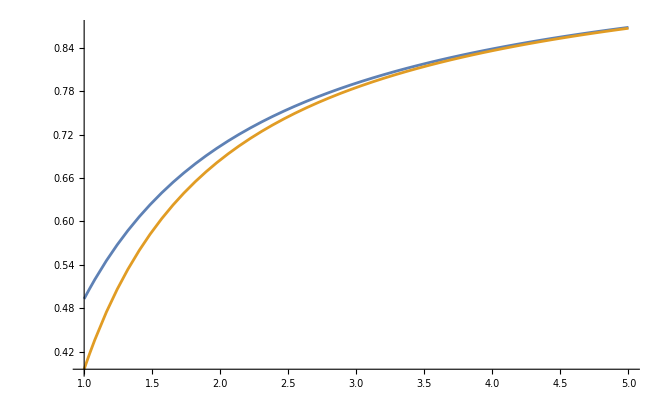

```mathematica
Plot[{Sp[1/2,x],Sm[1/2,x]},{x,1,5}]
```

```mathematica
N[{Sm[1/2,3],Sp[1/2,3]},10]
```

{0.7852685116,0.7913521713}

```mathematica
FullSimplify[Sum[f^n*g[1]^n/(2n(2n-1)),{n,1,∞}]]
```

√f ArcTanh[√f]+1/2 Log[1-f]